# Rayos de luz en d=5

## Schwarzschild

```mathematica
Clear[μ]
fSch[r_]:=1-μ/(3r^2)
FullSimplify[Integrate[1/fSch[r],r]]
```

r-(√μ ArcTanh[(√3 r)/(√μ)])/(√3)

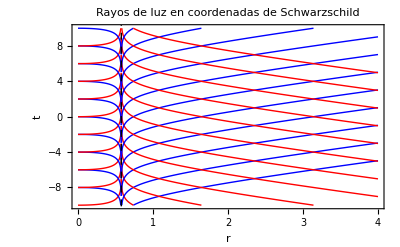

```mathematica
(*Definición de parámetros*)μ=1; (*Masa del agujero negro*)
rs=Sqrt[μ/3]; (*Radio de Schwarzschild*)

(*Coordenada de tortuga r**)
rSrStar[r_]:=r-(rs) Log[(r-rs)/(r+rs)]

(*Trayectorias de luz en Schwarzschild (t vs r)*)
(*t=constant\pm r**)
plotSchwarzschild=Plot[Evaluate[Table[{rStar[r]+c,-rStar[r]+c},{c,-10,10,2}]],{r,0,4},PlotRange->{{0,4},{-10,10}},PlotStyle->{Directive[Blue,Thin],Directive[Red,Thin]},Frame->True,FrameLabel->{"r","t"},PlotLabel->"Rayos de luz en coordenadas de Schwarzschild",Epilog->{Dashed,Black,InfiniteLine[{rs,0},{0,1}]}]
```